```mathematica
T0mat[h_]={{-2/h^3,1/h^2,1/h^2},
{3/h^2,-2/h,-1/h},
{0,1,0}};
Tmat[i_,h_]={{(-1+2 i)/(h^4 i^2),(-3-2 i)/(h^4 (1+i)^2),1/(h^3 i),1/(h^3 (1+i))},
{(2-6 i^2)/(h^3 i^2),(2 (2+6 i+3 i^2))/(h^3 (1+i)^2),-(2+3 i)/(h^2 i),(-1-3 i)/(h^2 (1+i))},
{((1+i) (-1-3 i+6 i^2))/(h^2 i^2),-(i (8+15 i+6 i^2))/(h^2 (1+i)^2),((1+i) (1+3 i))/(h i),(i (2+3 i))/(h (1+i))},
{-(2 (-1+i) (1+i)^2)/(h i),(2 i^2 (2+i))/(h (1+i)),-(1+i)^2,-i^2}};
```

```mathematica
Pbar[i_,h_]:={{-2/9 h^9 i^9+2/9 h^9 (1+i)^9,1/4 (-h^8 i^8+h^8 (1+i)^8),2/7 (-h^7 i^7+h^7 (1+i)^7),1/3 (-h^6 i^6+h^6 (1+i)^6)},
{1/4 (-h^8 i^8+h^8 (1+i)^8),2/7 (-h^7 i^7+h^7 (1+i)^7),1/3 (-h^6 i^6+h^6 (1+i)^6),2/5 (-h^5 i^5+h^5 (1+i)^5)},
{2/7 (-h^7 i^7+h^7 (1+i)^7),1/3 (-h^6 i^6+h^6 (1+i)^6),2/5 (-h^5 i^5+h^5 (1+i)^5),1/2 (-h^4 i^4+h^4 (1+i)^4)},
{1/3 (-h^6 i^6+h^6 (1+i)^6),2/5 (-h^5 i^5+h^5 (1+i)^5),1/2 (-h^4 i^4+h^4 (1+i)^4),2/3 (-h^3 i^3+h^3 (1+i)^3)}};
Ptmat[i_,h_]:={{(h (1-4 i-17 i^2+42 i^3+234 i^4))/(315 i^4),(h (-15 i-8 i^2+154 i^3+324 i^4+162 i^5))/(630 i^3 (1+i)^2),(h^2 (-4-i+60 i^2+132 i^3))/(1260 i^3)},
{(h (-15 i-8 i^2+154 i^3+324 i^4+162 i^5))/(630 i^3 (1+i)^2),(h (360 i^3+1560 i^4+2522 i^5+1788 i^6+468 i^7))/(630 i^3 (1+i)^4),(h^2 (30 i+127 i^2+180 i^3+78 i^4))/(1260 i^2 (1+i)^2)},
{(h^2 (-4-i+60 i^2+132 i^3))/(1260 i^3),(h^2 (30 i+127 i^2+180 i^3+78 i^4))/(1260 i^2 (1+i)^2),(h^3 (2+9 i+12 i^2))/(630 i^2)}}
```

```mathematica
Qbar[i_,h_]:={{24/7 (-h^7 i^7+h^7 (1+i)^7)+1/2 (-h^8 i^8+h^8 (1+i)^8),2 (-h^6 i^6+h^6 (1+i)^6)+4/7 (-h^7 i^7+h^7 (1+i)^7),4/5 (-h^5 i^5+h^5 (1+i)^5)+2/3 (-h^6 i^6+h^6 (1+i)^6),4/5 (-h^5 i^5+h^5 (1+i)^5)},
{4 (-h^6 i^6+h^6 (1+i)^6)+4/7 (-h^7 i^7+h^7 (1+i)^7),12/5 (-h^5 i^5+h^5 (1+i)^5)+2/3 (-h^6 i^6+h^6 (1+i)^6),-h^4 i^4+h^4 (1+i)^4+4/5 (-h^5 i^5+h^5 (1+i)^5),-h^4 i^4+h^4 (1+i)^4},
{24/5 (-h^5 i^5+h^5 (1+i)^5)+2/3 (-h^6 i^6+h^6 (1+i)^6),3 (-h^4 i^4+h^4 (1+i)^4)+4/5 (-h^5 i^5+h^5 (1+i)^5),-h^4 i^4+h^4 (1+i)^4+4/3 (-h^3 i^3+h^3 (1+i)^3),4/3 (-h^3 i^3+h^3 (1+i)^3)},
{6 (-h^4 i^4+h^4 (1+i)^4)+4/5 (-h^5 i^5+h^5 (1+i)^5),-h^4 i^4+h^4 (1+i)^4+4 (-h^3 i^3+h^3 (1+i)^3),2 (-h^2 i^2+h^2 (1+i)^2)+4/3 (-h^3 i^3+h^3 (1+i)^3),2 (-h^2 i^2+h^2 (1+i)^2)}};
Qtmat[i_,h_]:={{(h (3-20 i-16 i^2+312 i^3)-8 (1-4 i+4 i^2+63 i^4))/(210 h i^4),(h (-17+20 i+162 i^2+108 i^3)+8 (-3+4 i+67 i^2+126 i^3+63 i^4))/(210 h i^2 (1+i)^2),(h (-3+6 i+44 i^2)-2 (-4+i+14 i^2+231 i^3))/(210 i^3)},
{(h (-17+20 i+162 i^2+108 i^3)+8 (-3+4 i+67 i^2+126 i^3+63 i^4))/(210 h i^2 (1+i)^2),(h (305+948 i+952 i^2+312 i^3)-8 (72+264 i+382 i^2+252 i^3+63 i^4))/(210 h (1+i)^4),(h (17+46 i+26 i^2)+2 (12+50 i+56 i^2+21 i^3))/(210 i (1+i)^2)},
{(h (-3+6 i+44 i^2)-2 (-4+i+14 i^2+21 i^3))/(210 i^3),(h (17+46 i+26 i^2)+2 (12+50 i+56 i^2+21 i^3))/(210 i (1+i)^2),(h (h (3+8 i)-4 (2+7 i+14 i^2)))/(210 i^2)}}
```

```mathematica
(* make the entire P or Q matrix *)
makePorQ[N_,PorQbar_,PorQtmat_,tail_]:=Module[{h=1/N,res=ConstantArray[0,{2N,2N}]},
(* deal with the head, i=0 *)
Tmat0=T0mat[h];PorQbar0=PorQbar[0,h][[{2,3,4},{2,3,4}]];
res[[{1,N+1,N+2},{1,N+1,N+2}]]=Transpose[Tmat0].PorQbar0.Tmat0;
(* deal with the body, 0<i<N-1 *)
Do[Tmati=Tmat[i,h];PorQbari=PorQbar[i,h];
res[[{i,i+1,N+i+1,N+i+2},{i,i+1,N+i+1,N+i+2}]]+=Transpose[Tmati].PorQbari.Tmati,{i,1,N-2}];
(* deal with the tail, i=N-1 *)
res[[{N-1,N,2N},{N-1,N,2N}]]+=PorQtmat[N-1,h];
(* deal with the actual tail, i=N *)
res[[N,N]]+=tail;
res]
```

```mathematica
ψexact[r_]:=2r Exp[-r];
ψq[D_,C_,B_,A_,r_]:=D r+C r^2+B r^3+A r^4; (* q: quartic *)
ψt[rN_,ψN_,r_]:=ψN r/rN Exp[1-r/rN];(* t: tail *)
```

```mathematica
(* integrate the square of a function in an interval *)
intsqq[D_,C_,B_,A_,r0_,rh_]:=-1/3 D^2 r0^3-1/2 C D r0^4-(C^2 r0^5)/5-2/5 B D r0^5-1/3 B C r0^6-1/3 A D r0^6-(B^2 r0^7)/7-2/7 A C r0^7-1/4 A B r0^8-(A^2 r0^9)/9+(D^2 rh^3)/3+1/2 C D rh^4+(C^2 rh^5)/5+2/5 B D rh^5+1/3 B C rh^6+1/3 A D rh^6+(B^2 rh^7)/7+2/7 A C rh^7+1/4 A B rh^8+(A^2 rh^9)/9;
(* integrate the square of a function in the tail *)
(* Integrate[ψtail[rN,ψN,r]^2,{r,rN,Infinity},Assumptions->rN>0] *)
intsqt[rN_,ψN_]:=(5 rN ψN^2)/4;
```

```mathematica
normalN[ψ_,N_]:=Module[{h=1/N},res=0;
(* deal with the head, i=0 *)
{BB,CC,DD}=T0mat[h].ψ[[{1,N+1,N+2}]];
res+=intsqq[DD,CC,BB,0,0,h];
(* deal with the body, 0<i<N-1 *)
Do[{AA,BB,CC,DD}=Tmat[i,h].ψ[[{i,i+1,N+i+1,N+i+2}]];
res+=intsqq[DD,CC,BB,AA,i h,(i+1)h],{i,1,N-2}];
(* deal with the tail, i=N-1 *)
{AA,BB,CC,DD}=Tmat[N-1,h].(Join[ψ[[{N-1,N,2N}]],{0}]);
res+=intsqq[DD,CC,BB,AA,(N-1) h,1];
(* deal with the actual tail, i=N *)
res+=intsqt[1,ψ[[N]]];
1/Sqrt[res]];
```

```mathematica
renderN[ψ_,N_,r_]:=Module[{i=IntegerPart[r*N],h=1/N},
If[i≥N,res=ψt[1,ψ[[N]],r],];
If[i==0,{BB,CC,DD}=T0mat[h].ψ[[{1,N+1,N+2}]];res=ψq[DD,CC,BB,0,r],];
If[0<i<N-1,{AA,BB,CC,DD}=Tmat[i,h].ψ[[{i,i+1,N+i+1,N+i+2}]];
res=ψq[DD,CC,BB,AA,r],];
If[i==N-1,{AA,BB,CC,DD}=Tmat[N-1,h].(Join[ψ[[{N-1,N,2N}]],{0}]);
res=ψq[DD,CC,BB,AA,r]];
res]
```

```mathematica
ExploreN[NN_]:=Module[{},
myPP=makePorQ[NN,Pbar,Ptmat,5/2];
myQQ=makePorQ[NN,Qbar,Qtmat,5/2];
myHH=-Inverse[myPP].myQQ;
{myEE,myψψ}=Eigensystem[N[myHH,16]];
myE=myEE[[-1]];myψ=Sign[myψψ[[-1,NN+1]]]*normalN[myψψ[[-1]],NN]*myψψ[[-1]];
{myE,myψ}]
```

```mathematica
PlotN[NN_]:=Module[{},
myPP=makePorQ[NN,Pbar,Ptmat,5/2];
MatrixPlot[myPP]
myQQ=makePorQ[NN,Qbar,Qtmat,5/2];
MatrixPlot[myQQ]
myHH=-Inverse[myPP].myQQ;
MatrixPlot[myHH]
{myEE,myψψ}=Eigensystem[N[HH2,16]];
myE=myEE[[-2]];
myψ=Sign[myψψ[[-1,NN+1]]]*normalN[myψψ[[-1]],NN]*myψψ[[-1]];
Plot[{ψexact[r],renderN[myψ,NN,r]},{r,0,2}]
0]
```

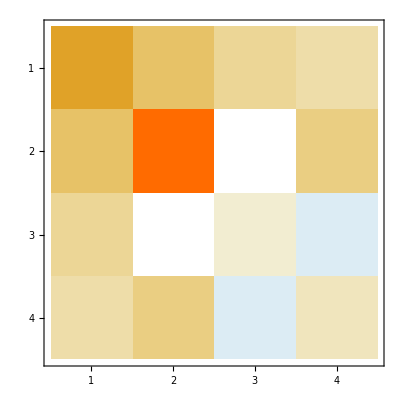

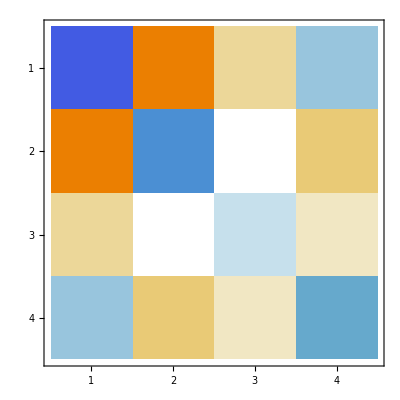

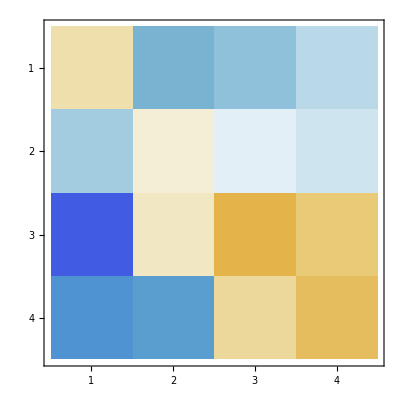

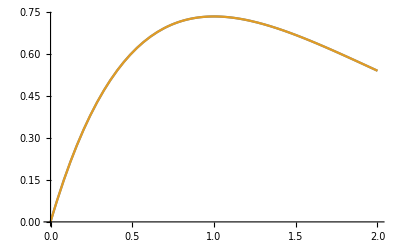

```mathematica
(* N = 2 case *)
NN=2;
myPP=makePorQ[NN,Pbar,Ptmat,5/2];
MatrixPlot[myPP]
myQQ=makePorQ[NN,Qbar,Qtmat,5/2];
MatrixPlot[myQQ]
myHH=-Inverse[myPP].myQQ;
MatrixPlot[myHH]
{myEE,myψψ}=Eigensystem[N[myHH,16]];
myE=myEE[[-1]];
myψ=Sign[myψψ[[-1,NN+1]]]*normalN[myψψ[[-1]],NN]*myψψ[[-1]];
Plot[{ψexact[r],renderN[myψ,NN,r]},{r,0,2}]
```

```mathematica
{E2,ψ2}=ExploreN[2]
{E3,ψ3}=ExploreN[3]
{E4,ψ4}=ExploreN[4]
{E5,ψ5}=ExploreN[5]
{E6,ψ6}=ExploreN[6]
{E7,ψ7}=ExploreN[7]
{E8,ψ8}=ExploreN[8]
```

{-0.9999965486040098,{0.606370810766,0.7357539980652,1.992355503735,0.60913090585}}

{-0.9999997391847512,{0.4776465902729,0.6845533619262,0.7357612939669,1.997521444951,0.9562320530872,0.3425112295337}}

{-0.9999999597962493,{0.389386287191,0.606529152958,0.708550730106,0.735759921003,1.99890669944,1.16857375327,0.606637786855,0.236219778417}}

{-0.9999999907495459,{0.327486277134,0.53625530072,0.658574255048,0.718926858231,0.735759343365,1.99942499562,1.31016275374,0.804439166609,0.439070297081,0.179741779698}}

{-0.9999999972421157,{0.282157592472,0.477687151142,0.60653077137,0.684556390616,0.724330611618,0.735759112279,1.99966116556,1.41091580481,0.955406661296,0.606542896635,0.342284984795,0.144870223835}}

{-0.99999999901404,{0.24767776004,0.42941537294,0.55837638323,0.64539225372,0.69934536537,0.72749645142,0.73575900886,1.9997838178,1.4861478755,1.0735586049,0.74450935371,0.48404857042,0.27974122793,0.12125144945}}

{-0.9999999995967981,{0.22062325102,0.38940025497,0.51546698169,0.606530721,0.66907686136,0.70854991198,0.72950861941,0.73575895747,1.9998537369,1.5444176208,1.1682141247,0.85911654182,0.60653363264,0.40144826483,0.23618495296,0.10421665518}}

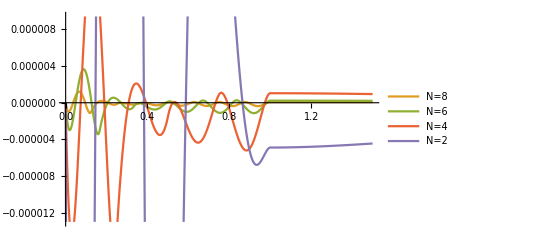

```mathematica
Plot[{renderN[ψ8,8,r]-ψexact[r],renderN[ψ6,6,r]-ψexact[r],renderN[ψ4,4,r]-ψexact[r],renderN[ψ2,2,r]-ψexact[r]},{r,0,3/2},
PlotStyle->{RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351]},PlotLegends->Placed[LineLegend[{"N=8","N=6","N=4","N=2"},LegendLayout->{"Column",2}],{Right,Top}]]
```

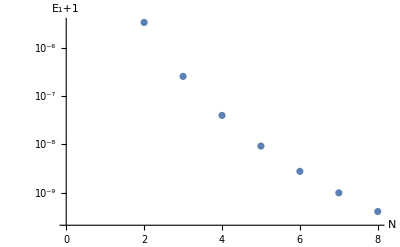

```mathematica
ListLogPlot[{Null,E2+1,E3+1,E4+1,E5+1,E6+1,E7+1,E8+1},AxesLabel->{N,Subscript["E",1]+1}]
```